```mathematica
(*Mathematica*)
```

```mathematica
Table[3,{i,5},{j,5}]
```

{{3,3,3,3,3},{3,3,3,3,3},{3,3,3,3,3},{3,3,3,3,3},{3,3,3,3,3}}

```mathematica
{{3,3,3,3,3},
{3,3,0,3,3},
{3,0,0,0,3},
{3,3,0,3,3},
{3,3,3,3,3}}
```

{{3,3,3,3,3},{3,3,0,3,3},{3,0,0,0,3},{3,3,0,3,3},{3,3,3,3,3}}

```mathematica
{{2,2,2,2,2,2,2},
{2,2,2,1,2,2,2},
{2,2,2,1,2,2,2},
{2,1,1,1,1,1,2},
{2,2,2,1,2,2,2},
{2,2,2,1,2,2,2},
{2,2,2,2,2,2,2}}
```

{{2,2,2,2,2,2,2},{2,2,2,1,2,2,2},{2,2,2,1,2,2,2},{2,1,1,1,1,1,2},{2,2,2,1,2,2,2},{2,2,2,1,2,2,2},{2,2,2,2,2,2,2}}

```mathematica
{{1,1,1,1,1,1,1},
{1,1,1,0,1,1,1},
{1,1,1,0,1,1,1},
{1,0,0,0,0,0,1},
{1,1,1,0,1,1,1},
{1,1,1,0,1,1,1},
{1,1,1,1,1,1,1}}
```

{{1,1,1,1,1,1,1},{1,1,1,0,1,1,1},{1,1,1,0,1,1,1},{1,0,0,0,0,0,1},{1,1,1,0,1,1,1},{1,1,1,0,1,1,1},{1,1,1,1,1,1,1}}

```mathematica
(*Hadamard Matrix self-similar recursive function*)
```

```mathematica
(*two level switch matrix recursive*)
```

```mathematica
Clear[HadamardMatrixa];

MatrixJoinH[A_,B_]:=Transpose[Join[Transpose[A],Transpose[B]]];

KroneckerProducta[M_,N_]:=Module[{M1,N1,LM,LN,N2},M1=M;
N1=N;
LM=Length[M1];
LN=Length[N1];
Do[M1[[i,j]]=M1[[i,j]]N1,{i,1,LM},{j,1,LM}];
Do[M1[[i,1]]=MatrixJoinH[M1[[i,1]],M1[[i,j]]],{j,2,LM},{i,1,LM}];
N2={};
Do[AppendTo[N2,M1[[i,1]]],{i,1,LM}];
N2=Flatten[N2];
Partition[N2,LM*LN,LM*LN]]
```

```mathematica
(*First level:5x5*)
```

```mathematica
HadamardMatrixa[2]:={{3,3,3,3,3},
{3,3,0,3,3},
{3,0,0,0,3},
{3,3,0,3,3},
{3,3,3,3,3}};
```

```mathematica
(*second level :11x11*)
```

```mathematica
HadamardMatrixa[n_]:=Module[{m},m={{2,2,2,2,2,2,2},
{2,2,2,1,2,2,2},
{2,2,2,1,2,2,2},
{2,1,1,1,1,1,2},
{2,2,2,1,2,2,2},
{2,2,2,1,2,2,2},
{2,2,2,2,2,2,2}};KroneckerProducta[m,HadamardMatrixa[n/2]]];
```

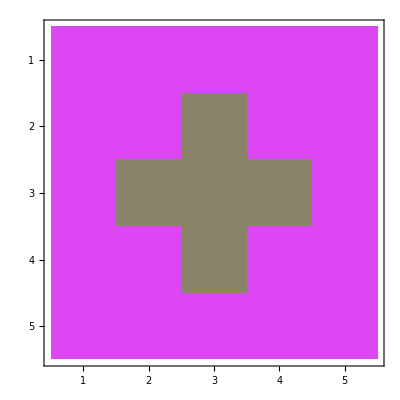
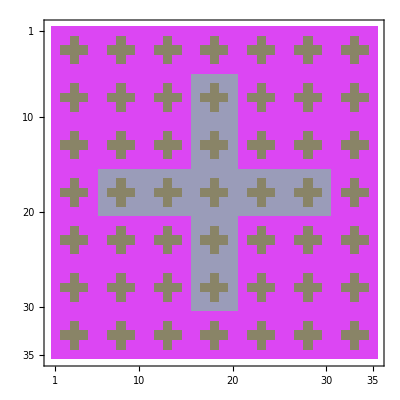
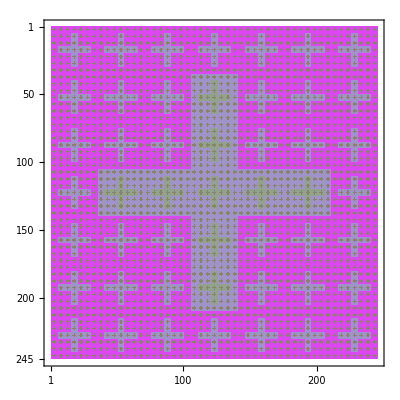

```mathematica
Table[MatrixPlot[HadamardMatrixa[2^n],Axes->False,ColorFunction->"AuroraColors"],{n,1,3}]
```

```mathematica
w=HadamardMatrixa[2^5];
```

```mathematica
Dimensions[w]
```

{12005,12005}

```mathematica
g1=MatrixPlot[w,Frame->False,Axes->False,ColorFunction->Hue,ImageSize->{6002,6002}];
```

```mathematica
Export["Hadamard_twolevel_cross_carpet5and7_level5_6002_Hue_colors.jpg",g1]
```

Hadamard_twolevel_cross_carpet5and7_level5_6002_Hue_colors.jpg

```mathematica
(*end*)
```